## Book Problem

### Chapter 9, Problem 1

InterpolatingFunction[…][x]

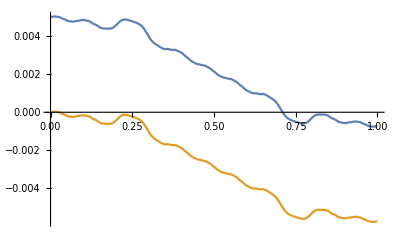

```mathematica
GN[x_,y_]=Piecewise[{{x-y, 0<y&&y<x}, {0, x<y&&y<1}}];
f[x_]=Sin [2π Sin[4π Sin[2π x]]];
val=NDSolveValue[
{u''[x]==f[x],
u'[0]==0,
u[0]==0.005},u[x],{x,0,1}]
Plot[{val,NIntegrate[GN[x,y]f[y],{y,0,1}]},
{x,0,1}]
```

## Additional Problems

### Problem 1

```mathematica
DEigensystem[{-∇_{x,y}^2 u[x,y],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Rectangle[{0,1},{0,1}],10]
```

```mathematica
DEigensystem[{-Derivative[0,2][u][x,y]-Derivative[2,0][u][x,y],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Rectangle[{0,0}],20]ᵀ//MatrixForm
```

(2 π^2 | Sin[π x] Sin[π y]
5 π^2 | Sin[2 π x] Sin[π y]
5 π^2 | Sin[π x] Sin[2 π y]
8 π^2 | Sin[2 π x] Sin[2 π y]
10 π^2 | Sin[3 π x] Sin[π y]
10 π^2 | Sin[π x] Sin[3 π y]
13 π^2 | Sin[3 π x] Sin[2 π y]
13 π^2 | Sin[2 π x] Sin[3 π y]
17 π^2 | Sin[4 π x] Sin[π y]
17 π^2 | Sin[π x] Sin[4 π y]
18 π^2 | Sin[3 π x] Sin[3 π y]
20 π^2 | Sin[4 π x] Sin[2 π y]
20 π^2 | Sin[2 π x] Sin[4 π y]
25 π^2 | Sin[4 π x] Sin[3 π y]
25 π^2 | Sin[3 π x] Sin[4 π y]
26 π^2 | Sin[5 π x] Sin[π y]
26 π^2 | Sin[π x] Sin[5 π y]
29 π^2 | Sin[5 π x] Sin[2 π y]
29 π^2 | Sin[2 π x] Sin[5 π y]
32 π^2 | Sin[4 π x] Sin[4 π y])

```mathematica
Assuming[m>0&&m∈Integers&&n>0&&n∈Integers&&L>0,∫_0^1 ∫_0^1 (Sin[m π x]^2 Sin[n π y]^2)ⅆxⅆy//FullSimplify]
Assuming[m>0&&m∈Integers&&n>0&&n∈Integers&&j>0&&j∈Integers&&k>0&&k∈Integers,∫_0^1 ∫_0^1 (Sin[m π x]Sin[n π y]Sin[j π x]Sin[k π y])ⅆxⅆy//FullSimplify]
```

1/4

0

### Problem 2

#### (b)

```mathematica
Assuming[n∈Integers&&n>0&&α>0,DSolveValue[{r^2 R''[r]+r R'[r]==(n^2 π^2)/α^2 R[r],R[1]==1},R[r],{r,0,1}]]//FullSimplify
```

Cosh[(n π Log[r])/α]+ⅈ C[2] Sinh[(n π Log[r])/α]

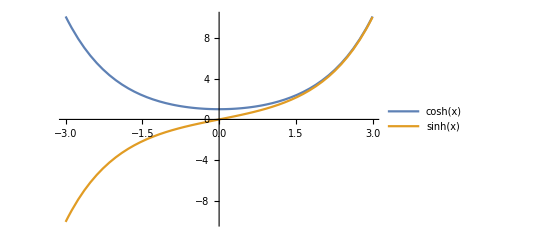

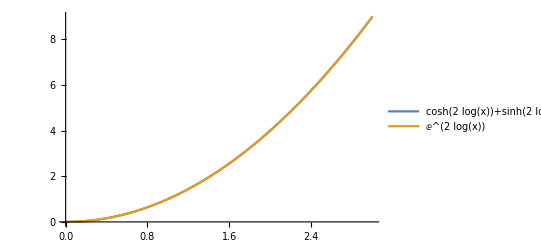

```mathematica
Plot[{Cosh[x],Sinh[x]},{x,-3,3},PlotLegends->"Expressions"]
Plot[{Cosh[2Log[x]]+Sinh[2Log[x]],ⅇ^(2Log[x])},{x,0,3},PlotLegends->"Expressions"]
```

#### (d)

```mathematica
Assuming[n∈Integers&&n>0,2/(π/4)∫_0^(π/4) (Sin[4n θ]θ(π/4-θ))ⅆθ//FullSimplify]
```

-(-1+(-1)^n)/(4 n^3 π)

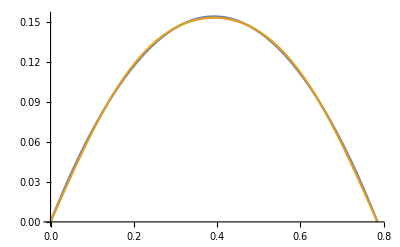

```mathematica
Plot[{θ(π/4-θ),∑_(n=1)^3 (-(-1+(-1)^n)/(4 n^3 π))Sin[4n θ]},{θ,0,π/4}]
```

```mathematica
-(-1+(-1)^n)/(4 n^3 π)/.n->5
```

1/(250 π)

```mathematica
DiscretePlot3D[(x-y)/y^3,{x,1,100},{y,1,5},RegionFunction->Function[{x,y},x>y],PlotRange->All]
```

-Graphics3D-

### Problem 3

#### (b)

```mathematica
Assuming[t>0&&TMP>=0,∫_0^t 1/(4π τ)^(3/2)ⅇ^(-Norm[x-y]^2/(4τ))ⅆτ]
```

Erfc[Norm[x-y]/(2 √t)]/(4 π Norm[x-y])

#### (c)

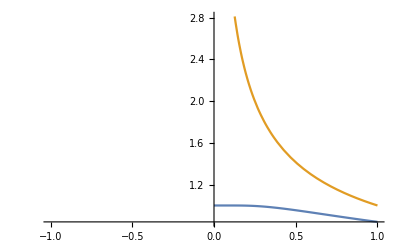

t/(4 π^(3/2))+O[t]^3

```mathematica
Plot[{Erf[1/(√x)],1/√x},{x,-1,1}]
Series[Erf[Norm[x-y]/2 t]/(4π Norm[x-y]),{t,0,2}]
```

```mathematica
D[(Erf[Norm[x-y]/(2 √t)]/(4π Norm[x-y])f[y]), t]/D[(1/(√t)), t]
```

(ⅇ^(-Norm[x-y]^2/(4 t)) f[y])/(4 π^(3/2))